```mathematica
α=2;
β=2;
γ=2;
Subscript[h, 0]=0;
Subscript[h, 1]=2;
Subscript[h, 2]=4;
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 0]*)Subscript[A, 0]={{Exp[k Subscript[h, 0]], Exp[-k Subscript[h, 0]]},{k Exp[k Subscript[h, 0]], -k Exp[-k Subscript[h, 0]]}};(*matriz Subscript[A, 0]*)
Subscript[CA, 0]={{1,0},{- α,1}};(*matriz de condiciones de frontera*)
Subscript[CD, 00]={{Subscript[c, 0]},{0}};(*Matriz semilla*)
Subscript[A, 00]=Inverse[Subscript[A, 0]] . Subscript[CA, 0] . Subscript[A, 0] ;(*Matriz Subscript[M, 0]*)
```

```mathematica
(*Subscript[A, 00][[1,1]]
Subscript[A, 00][[2,1]]*)
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 1]*)Subscript[A, 1]={{Exp[k Subscript[h, 1]], Exp[-k Subscript[h, 1]]},{k Exp[k Subscript[h, 1]], -k Exp[-k Subscript[h, 1]]}};(*matriz Subscript[A, 0]*)
Subscript[CA, 1]={{1,0},{-β,1}};(*matriz de condiciones de frontera*)
Subscript[A, 11]=Inverse[Subscript[A, 1]] . Subscript[CA, 1] . Subscript[A, 1] ;(*Matriz Subscript[M, 0]*)
(*Subscript[A, 11][[1,1]]//Simplify
Subscript[A, 11][[2,1]]//Simplify*)
```

```mathematica
(*Caso discontinuidad en x=Subscript[h, 2]*)Subscript[A, 2]={{Exp[k Subscript[h, 2]], Exp[-k Subscript[h, 2]]},{k Exp[k Subscript[h, 2]], -k Exp[-k Subscript[h, 2]]}};(*matriz Subscript[A, 0]*)
Subscript[CA, 2]={{1,0},{-γ,1}};(*matriz de condiciones de frontera*)
Subscript[A, 22]=Inverse[Subscript[A, 2]] . Subscript[CA, 2] . Subscript[A, 2] . Subscript[A, 11] . Subscript[A, 00] . Subscript[CD, 00];(*Matriz Subscript[M, 0]*)
```

```mathematica
Subscript[A, 22][[1,1]]//Simplify(*Elemento correspondiente al término para la ecuación de dispersión*)
Subscript[A, 22][[2,1]]//Simplify
```

(ⅇ^(-8 k) (-1-2 ⅇ^(4 k) (-1+k)+ⅇ^(8 k) (-1+k)^3-k) c_0)/k^3

((ⅇ^(8 k) (-1+k)^2+(1+k)^2+ⅇ^(4 k) (-2+k^2)) c_0)/k^3

```mathematica
κ[k_]:=(ⅇ^(-8 k) (-1-2 ⅇ^(4 k) (-1+k)+ⅇ^(8 k) (-1+k)^3-k) Subscript[c, 0])/k^3;(*Define la ecuación de dispersión*)
NSolve[κ[k]==0,k,Reals](*Obtiene eigen-valores*)
```

{{k→0.980173},{k→-0.901917},{k→0.649819},{k→1.14763}}

```mathematica
kj={1.147626322393826,0.9801725987182216,0.6498190795900394};(*Arreglo de k permitidos*)
ϕj[x_,n_]:=Piecewise[{{Exp[kj[[n]]x] ,x<0},{(1-1/kj[[n]])  Exp[kj[[n]]x]+(1/kj[[n]])Exp[-kj[[n]]x] ,0<x<Subscript[h, 1]},{((ⅇ^(-4 kj[[n]])(-1+ⅇ^(4 kj[[n]]) (-1+kj[[n]])^2))/(kj[[n]])^2 ) Exp[kj[[n]]x]+((1+ⅇ^(4 kj[[n]]) (-1+kj[[n]])+kj[[n]])/(kj[[n]])^2)Exp[-kj[[n]]x] ,Subscript[h, 1]<x<Subscript[h, 2]},{(1/(kj[[n]])^3(ⅇ^(8 kj[[n]]) (-1+kj[[n]])^2+(1+kj[[n]])^2+ⅇ^(4 kj[[n]]) (-2+(kj[[n]])^2)))Exp[-kj[[n]]x] ,x>Subscript[h, 2]}}];
(*Definición de la eigen-función*)
```

```mathematica
Mj[n_]:=√(∫_(-∞)^0 (Abs[ϕj[x,n]])^2 ⅆx+∫_0^Subscript[h, 1] (Abs[ϕj[x,n]])^2 ⅆx+∫_Subscript[h, 1]^Subscript[h, 2] (Abs[ϕj[x,n]])^2 ⅆx+∫_Subscript[h, 2]^∞ (Abs[ϕj[x,n]])^2 ⅆx);(*Define las constantes de normalización*)
Mj[1]
Mj[2]
Mj[3]
(*Obtenemos el elemento correspondiente para generar el arreglo de constantes de normalización*)
```

1.95689

1.38442

1.96054

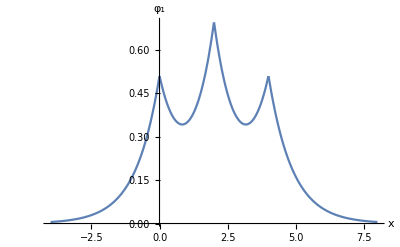

```mathematica
M={1.9568921401876602,1.384424405255327,1.9605365798481644};(*Constantes de normalización de cada eigen-función*)
Plot[1/M[[1]] ϕj[x,1],{x,-4,8},PlotRange->All,AxesLabel->{Style[x,Medium],Style[Subscript[φ, 1],Medium]}](*Gráfica de la eigen-función*)
```

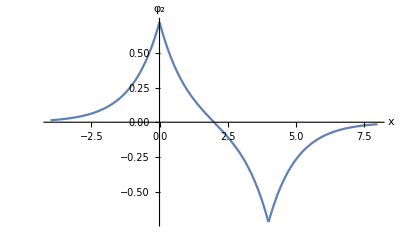

```mathematica
Plot[1/M[[2]] ϕj[x,2],{x,-4,8},PlotRange->All,AxesLabel->{Style[x,Medium],Style[Subscript[φ, 2],Medium]}]
```

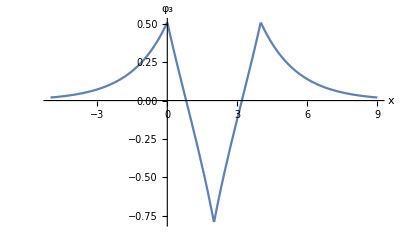

```mathematica
Plot[1/M[[3]] ϕj[x,3],{x,-5,9},PlotRange->All,AxesLabel->{Style[x,Medium],Style[Subscript[φ, 3],Medium]}]
```

```mathematica
(1-1/k)  Exp[k x]+(1/k)Exp[-k x]//Simplify
```

(ⅇ^(-k x) (1+ⅇ^(2 k x) (-1+k)))/k

```mathematica
((ⅇ^(-4 k)(-1+ⅇ^(4 k) (-1+k)^2))/k^2 ) Exp[k x]+((1+ⅇ^(4 k) (-1+k)+k)/k^2)Exp[-k x]//ExpToTrig
```

((1+k+(-1+k) (Cosh[4 k]+Sinh[4 k])) (Cosh[k x]-Sinh[k x]))/k^2+((-1+(-1+k)^2 (Cosh[4 k]+Sinh[4 k])) (Cosh[4 k-k x]-Sinh[4 k-k x]))/k^2

```mathematica
(1/k^3(ⅇ^(8 k) (-1+k)^2+(1+k)^2+ⅇ^(4 k) (-2+k^2)))Exp[-k x]//Simplify
```

(ⅇ^(-k x) (ⅇ^(8 k) (-1+k)^2+(1+k)^2+ⅇ^(4 k) (-2+k^2)))/k^3